```mathematica
quit[]
(* Variable declarations *)
mt=0.18;(*kg*)
mw=0.1;(*kg*)
la=0.35;(*cm*)
lw=0.28;(*cm*)
lh=0.2475;(*cm*)
kf=0.61029972;(**)
mf = 0.09;(*kg*)
(* Setting UP matrices *)
A = {{0, 1, 0 ,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}};
MatrixForm[A]
```

quit[]

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
B = {{0,0,0},{(kf*lh)/(2*mf*lh*lh), (-kf*lh)/(2*mf*lh*lh),0}, {0,0,0}, {(kf*la)/((mt*la*la)+(mw*lw*lw)), (kf*la)/((mt*la*la)+(mw*lw*lw)),1/((mt*la*la)+(mw*lw*lw))}};
MatrixForm[B]
```

(0 | 0 | 0
13.6992 | -13.6992 | 0
0 | 0 | 0
7.14637 | 7.14637 | 33.456)

```mathematica
Cm = {{1,0,0,0},{0,0,1,0}};
MatrixForm[Cm]
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
Dm = {{0,0},{0,0}};
MatrixForm[Dm]
```

(0 | 0
0 | 0)

```mathematica
(*Obtaining the eigenvalues and vector*)
Eigenvalues[A]
```

{0,0,0,0}

```mathematica
Eigenvectors[A]
```

{{0,0,1,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*We have 4 repeated eigenvalues*)
(*Plotting to see the response of the system for a step input, Uf = Ub = 1* and assuming that we were initially at equilibrium, therefore X0 = {0,0,-40deg,0}*)
u[t_]:= {1,1,Cos[t]};
X0 = Transpose[{0,0,(320*Pi)/180, 0}];
MatrixForm[X0]
```

(0
0
(16 π)/9
0)

```mathematica
Xs[t] = MatrixExp [t A].X0 + ∫_0^t MatrixExp[(t - τ)A].B.u [τ]ⅆτ//Simplify//Chop;
MatrixForm[Xs[t]]
```

(0
0
39.0411+7.14637 t^2-33.456 Cos[t]
14.2927 t+33.456 Sin[t])

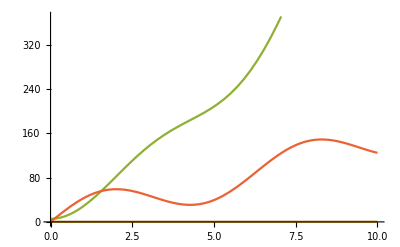

```mathematica
Plot[Evaluate[Xs[t]],{t,0,10}]
```

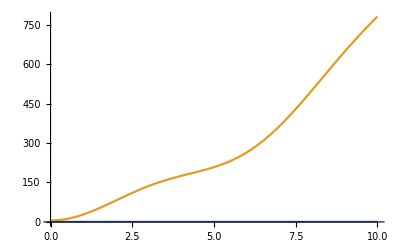

```mathematica
(*PLotting the output*)
Y[t] = Cm.Xs[t];
Plot[Evaluate[Y[t]],{t,0,10}]
```

```mathematica
(*Checking Controllability*)
A1 = A.B;
MatrixForm[A1]
A2 = A.A1;
MatrixForm[A2]
A3 = A.A2;
MatrixForm[A3]
```

(13.6992 | -13.6992 | 0.
0. | 0. | 0.
7.14637 | 7.14637 | 33.456
0. | 0. | 0.)

(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.)

(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.)

```mathematica
MatrixForm[B]
```

(0 | 0 | 0
13.6992 | -13.6992 | 0
0 | 0 | 0
7.14637 | 7.14637 | 33.456)

```mathematica
P = Join[B, A.B, A.A.B, A.A.A.B,2];
MatrixForm[P]
```

(0 | 0 | 0 | 13.6992 | -13.6992 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
13.6992 | -13.6992 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 7.14637 | 7.14637 | 33.456 | 0. | 0. | 0. | 0. | 0. | 0.
7.14637 | 7.14637 | 33.456 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
MatrixRank[P]
```

4

```mathematica
(*Since the rank of P is equal to N, then the system is controllable*)
(*Checking Observability *)
MatrixForm[Transpose[Cm]]
A4 = Transpose[A] . Transpose[Cm];
MatrixForm[A4]
A5 = Transpose[A.A]. Transpose[Cm];
MatrixForm[A5]
A6 = Transpose[A.A.A]. Transpose[Cm];
MatrixForm[A6]
```

(1 | 0
0 | 0
0 | 1
0 | 0)

(0 | 0
1 | 0
0 | 0
0 | 1)

(0 | 0
0 | 0
0 | 0
0 | 0)

(0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
Q = Join[Transpose[Cm],A4,A5,A6,2];
MatrixForm[Q]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
MatrixRank[Q]
```

4

```mathematica
(*The System is fully observalbe*)
(*Attempting to design a state feedback controller using *)
MatrixForm[A]
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
K = {{K11,K12,K13,K14},{K21,K22,K23,K24},{k31,k32,k33,k34}};
MatrixForm[K]
```

(K11 | K12 | K13 | K14
K21 | K22 | K23 | K24
k31 | k32 | k33 | k34)

```mathematica
λ = {λ1,λ2,λ3,λ4};
MatrixForm[λ]
I4 = IdentityMatrix[4];
MatrixForm[I4]
```

(λ1
λ2
λ3
λ4)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
n=4;
r=3;
```

```mathematica
Xsf = Join[I4 ℒ -A,B,2]; MatrixForm[Xsf] (*Where ℒ is here temporarily until we handle λ*)
```

(ℒ | -1 | 0 | 0 | 0 | 0 | 0
0 | ℒ | 0 | 0 | 13.6992 | -13.6992 | 0
0 | 0 | ℒ | -1 | 0 | 0 | 0
0 | 0 | 0 | ℒ | 7.14637 | 7.14637 | 33.456)

```mathematica
υ = Transpose[NullSpace[Xsf]] //Chop;
MatrixForm[υ]
```

(0 | 13.6992/ℒ^2 | -13.6992/ℒ^2
0 | 13.6992/ℒ | -13.6992/ℒ
-33.456/ℒ^2 | -7.14637/ℒ^2 | -7.14637/ℒ^2
-33.456/ℒ | -7.14637/ℒ | -7.14637/ℒ
0 | 0 | 1.
0 | 1. | 0
1. | 0 | 0)

```mathematica
Ψ = Take[υ,n];
MatrixForm[Ψ]
```

(0 | 13.6992/ℒ^2 | -13.6992/ℒ^2
0 | 13.6992/ℒ | -13.6992/ℒ
-33.456/ℒ^2 | -7.14637/ℒ^2 | -7.14637/ℒ^2
-33.456/ℒ | -7.14637/ℒ | -7.14637/ℒ)

```mathematica
ϝ = Take[υ,-r];
MatrixForm[ϝ]
```

(0 | 0 | 1.
0 | 1. | 0
1. | 0 | 0)

```mathematica
(*Now this was generally how the Ψ should look, and we need to substitute λ with each value once then join that matrix. In the tut/lec, we would add the eigenvalues before getting ψ and ϝ, but doing this beforehand wont affect anything mathematically*)
(*Adding the symbolic values of λ in order to get the full correct matrix we need*)
```

```mathematica
min=10000000000000;
λ={-102.9999,-102.9997,-102.9996,-12.9995};
Ω = Join[Ψ /. ℒ -> λ[[1]],Ψ /. ℒ -> λ[[2]],Ψ /. ℒ -> λ[[3]],Ψ /. ℒ -> λ[[4]],2];
Λ = Join[ϝ /. ℒ -> λ[[1]],ϝ /. ℒ -> λ[[2]],ϝ /. ℒ -> λ[[3]],ϝ /. ℒ -> λ[[4]],2];
selected = {s1,s2,s3,s4};
For[i=1,i<9,i++,
For[j=1,j<9,j++,
For[o=1,o<9,o++,
For[h=1,h<9,h++,
columnChoice = {i,j,o,h};
G = Ω[[All,columnChoice]];
𝒥 = Λ[[All, columnChoice]];
If[i==j || i==o || i==h || j==o || j==h || h==o,Continue,
If[0<Abs[Det[G]]<min,selected = columnChoice; min=Det[G];Print[min],Continue]
]
]
]
]
]
Print[selected]
```

1.49105×10^-29

5.45605×10^-30

{1,3,5,8}

```mathematica
G = Ω[[All,selected]];
𝒥 = Λ[[All, selected]];
K = 𝒥 . Inverse[Rationalize[G,10^-16]];
MatrixForm[K]
```

(1.97281×10^15 | 1.91535×10^13 | 3.78177×10^15 | 3.67163×10^13
1.97281×10^15 | 1.91535×10^13 | 3.78177×10^15 | 3.67163×10^13
-8.42804×10^14 | -8.18257×10^12 | -1.61561×10^15 | -1.56856×10^13)

{-113.707,-102.999,-91.3906,-1.34134}

(0 | 0 | 0
13.6992 | -13.6992 | 0
0 | 0 | 0
7.14637 | 7.14637 | 33.456)

(1 | 1 | 1
1 | 1 | 1
1 | 1 | 1)

(-19.0213-636.17 ⅇ^(-113.707 t)+1.37566 ⅇ^(-102.999 t)+791.848 ⅇ^(-91.3906 t)-132.011 ⅇ^(-1.34134 t)-6.02127 Cos[t]-4.67668 Sin[t]
72336.7 ⅇ^(-113.707 t)-141.692 ⅇ^(-102.999 t)-72367.4 ⅇ^(-91.3906 t)+177.071 ⅇ^(-1.34134 t)-4.67668 Cos[t]+6.02127 Sin[t]
10.6289+329.037 ⅇ^(-113.707 t)+5.62613 ⅇ^(-102.999 t)-416.777 ⅇ^(-91.3906 t)+73.703 ⅇ^(-1.34134 t)+3.36631 Cos[t]+2.61112 Sin[t]
-37413.7 ⅇ^(-113.707 t)-579.485 ⅇ^(-102.999 t)+38089.5 ⅇ^(-91.3906 t)-98.8605 ⅇ^(-1.34134 t)+2.61112 Cos[t]-3.36631 Sin[t])

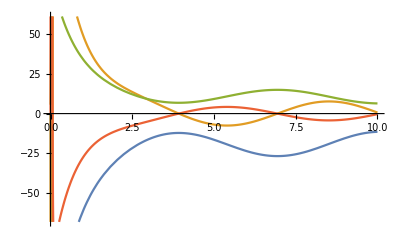

```mathematica
(*Plotting to see the response again*)
An = A-B.K;
Eigenvalues[An]
MatrixForm[B]
F ={{1,1,1},{1,1,1},{1,1,1}};
MatrixForm[F]
Bn = B.F;
v[t_]:= {1,1,Cos[t]};
Xc[t] = MatrixExp [t An].X0 + ∫_0^t MatrixExp[(t - τ)An].Bn.v[τ] ⅆτ//Simplify//Chop;
MatrixForm[Xc[t]]
Plot[Evaluate[Xc[t]],{t,0,10}]
```

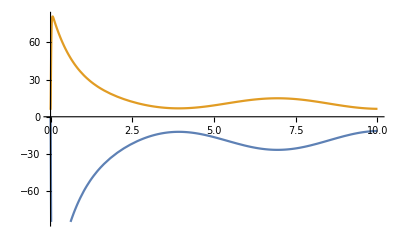

```mathematica
Yc[t] = Cm.Xc[t];
Plot[Evaluate[Yc[t]],{t,0,10}]
```